```mathematica
Remove["Global`*"](*Clears all variables*)
```

```mathematica
SetOptions[Plot,BaseStyle->{FontFamily->"Arial",FoSize->18},PlotStyle->{{Red,Thick},{Blue,Thick},{Black,Thick},{Orange,Thick},{Magenta,Thick}},TicksStyle->Directive[Black,10],Frame->True];
```

### Units

```mathematica
nm=10^-9 (*meter*);
MHz=10^6 (*hertz*);
GHz=10^9;
mW=10^-3(*watt*);
μs=10^-6(*second*);
ℏ=1.054571628 10^-34(*Joules seconds*);
```

### Calculations

```mathematica
Clear[λp,λs,Ωp,Ωs,H,SE,PSoln,ϕp,ϕs,Γ];
init=P[0]=={1,0,0,0};
P[t_]={p1[t],p2[t],p3[t],p4[t]}(*population in Feshbach, v=26 excited, and rovibrational states*);
padding={{70, 10}, {50, 10}}; (*padding, aspect ratio, and size set each plot to occupy the same space on screen. *)
aratio=0.5;
size=500;
Ωp=44 MHz;
Ωs=230 MHz;
Ωpp=√12 Ωp;
Γ=100 MHz;
Δp=21 GHz;
findSol[Δs0_]:=Module[{Δs=Δs0},
H[t_]=2π({{0, 1/2 Ωp, 1/2 Ωpp, 0}, {1/2 Ωp, Δp-ⅈ Γ/2, 0, 1/2 Ωs}, {1/2 Ωpp, 0, Δp+3GHz-ⅈ Γ/2, 0}, {0, 1/2 Ωs, 0, Δp-(21GHz+Δs)}})(*3-level Hamiltonian*);
SE=ⅈ P'[t]==H[t].P[t](*Schrodinger equation*);
PSoln=NDSolve[{SE,init},{p1,p2,p3,p4},{t,0,6 μs}];
Plot[{Evaluate[Abs[p1[t]]^2/.PSoln],Evaluate[Abs[p2[t]]^2/.PSoln],Evaluate[Abs[p3[t]]^2/.PSoln],Evaluate[Abs[p4[t]]^2/.PSoln],Evaluate[1-Abs[p1[t]]^2-Abs[p2[t]]^2-Abs[p3[t]]^2-Abs[p4[t]]^2/.PSoln]},{t,0,6 μs},ImagePadding->padding,ImageSize->size,AspectRatio-> aratio,FrameLabel->{"Time (μs)",""},PlotLegends->Placed[LineLegend[{"Initial","Int.","Det. Int","Final","Loss"},LabelStyle->18],{0.8,.5}],PlotLabel->StringForm["Δs=``",Δs]]]
```

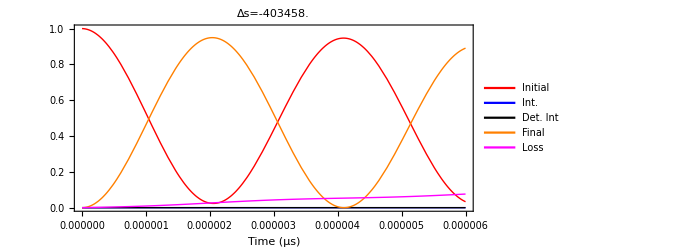
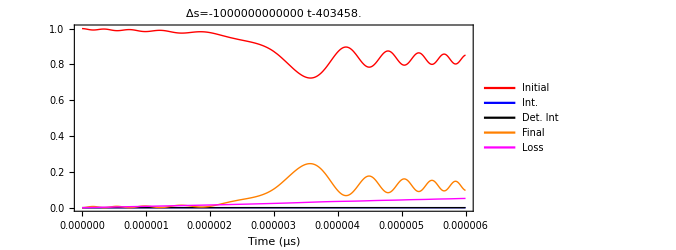
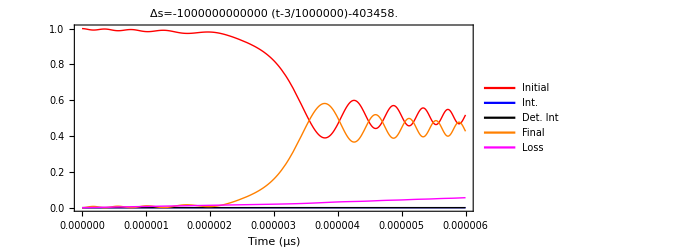
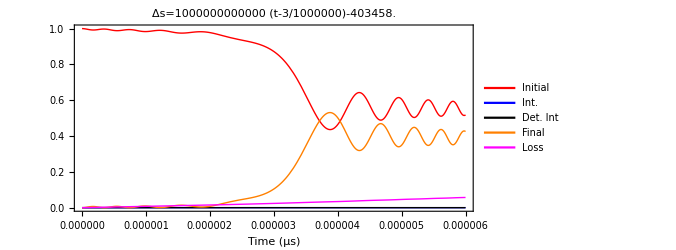

```mathematica
{findSol[-2.535/(2π)MHz],findSol[-2.535/(2π)MHz-Abs[MHz^2 (t-3μs)]],findSol[-2.535/(2π)MHz-MHz^2 (t-3μs)],findSol[-2.535/(2π)MHz+MHz^2 (t-3μs)]}
```

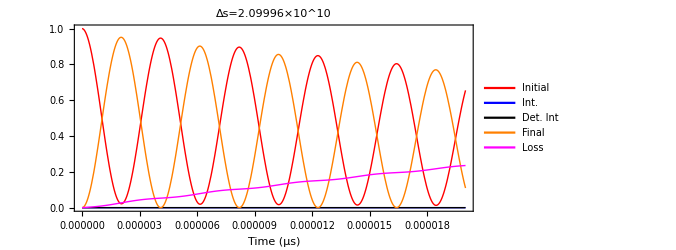
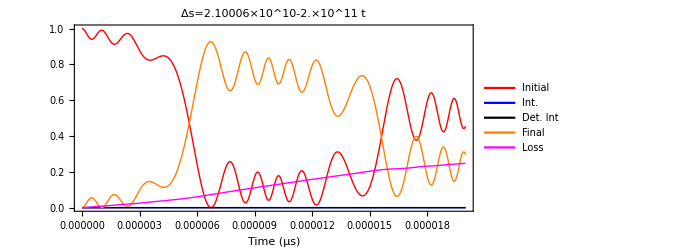
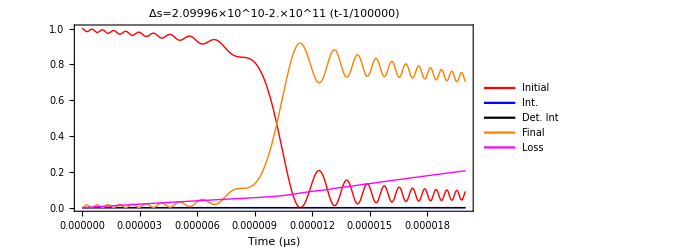
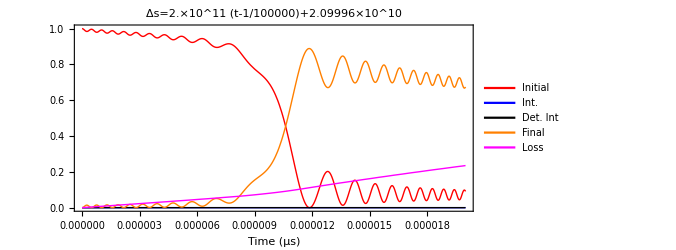

```mathematica
{findSol[21GHz-2.525/(2π)MHz],findSol[21 GHz-2.525/(2π)MHz+1MHz-Abs[.2 MHz^2 (t-10μs)]],findSol[21 GHz-2.525/(2π)MHz-.2 MHz^2 (t-10μs)],findSol[21 GHz-2.525/(2π)MHz+.2 MHz^2 (t-10μs)]}
```

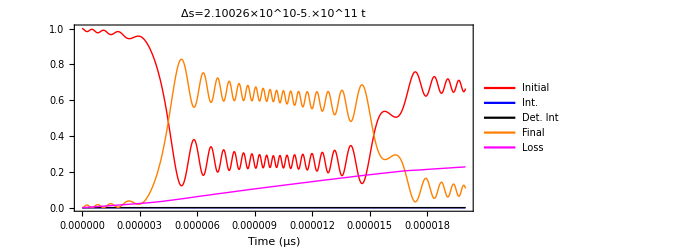
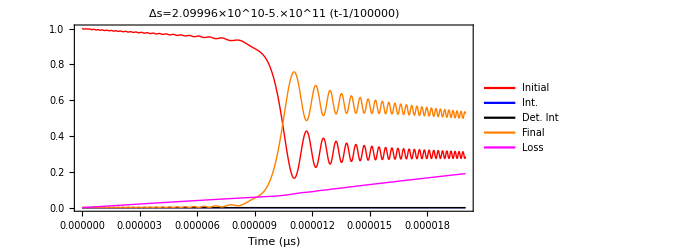
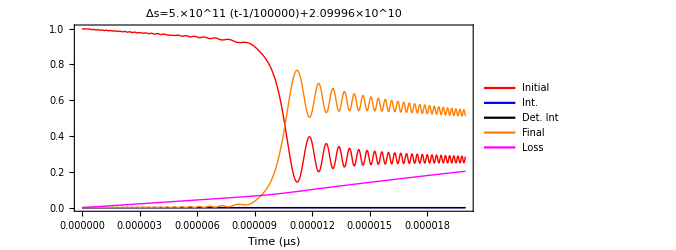
{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
{findSol[21GHz-2.525/(2π)MHz],findSol[21 GHz-2.525/(2π)MHz+3MHz-Abs[.5 MHz^2 (t-10μs)]],findSol[21 GHz-2.525/(2π)MHz-.5 MHz^2 (t-10μs)],findSol[21 GHz-2.525/(2π)MHz+.5 MHz^2 (t-10μs)]}
```

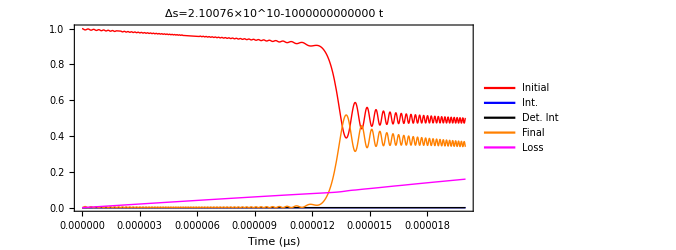
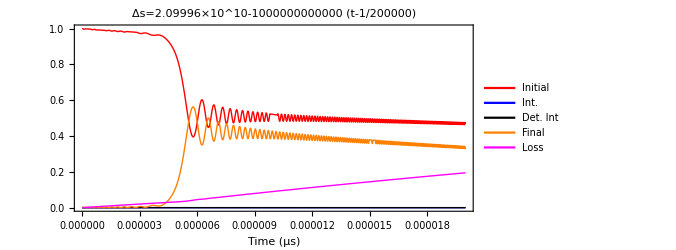
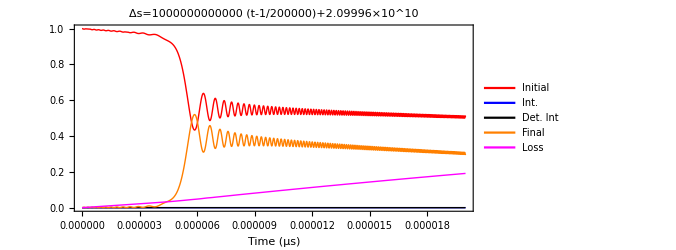
{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
{findSol[21GHz-2.525/(2π)MHz],findSol[21 GHz-2.525/(2π)MHz+8MHz-Abs[MHz^2 (t-5μs)]],findSol[21 GHz-2.525/(2π)MHz-MHz^2 (t-5μs)],findSol[21 GHz-2.525/(2π)MHz+MHz^2 (t-5μs)]}
```

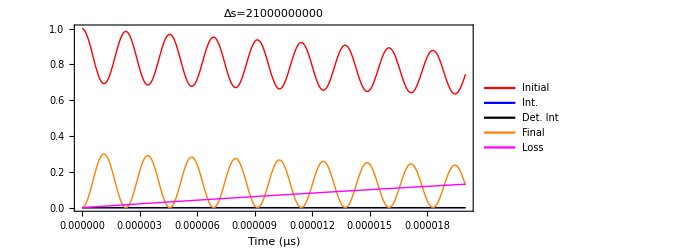
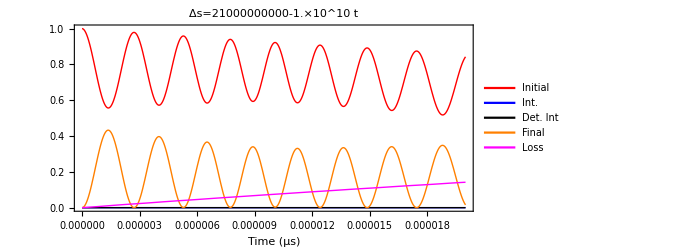
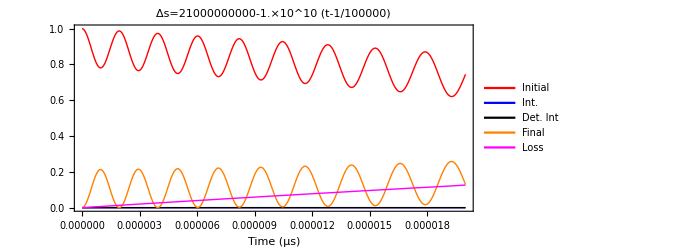
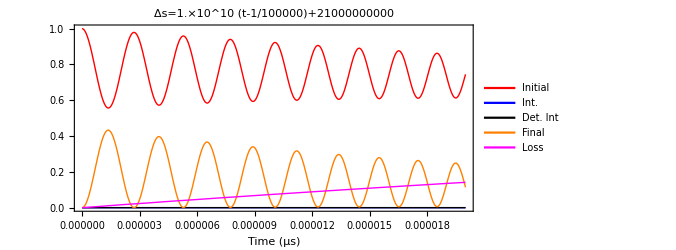

```mathematica
{findSol[21 GHz],findSol[21 GHz-Abs[.01 MHz^2 (t-10μs)]],findSol[21 GHz-.01 MHz^2 (t-10μs)],findSol[21 GHz+.01 MHz^2 (t-10μs)]}
```